```mathematica
f1[z_]:=(z^4(z-1)^2)/(z-(11-2√10)/18)  1/0.06519896529044934
f2[z_]:=(z^4(z-1)^2)/(z-(11+2√10)/18) 1/-0.10470513812995545
```

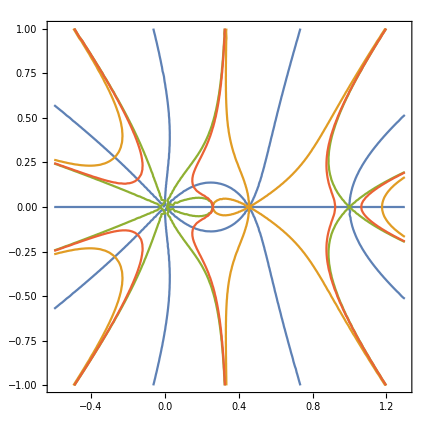

```mathematica
ContourPlot[{Im[f1[x+ⅈ y]]==-0.000001,Re[f1[x+ⅈ y]]==1,Re[f1[x+ⅈ y]]==0,Re[f1[x+ⅈ y]]==0.1},{x,-0.6,1.3},{y,-1,1},PerformanceGoal->"Quality"]
```

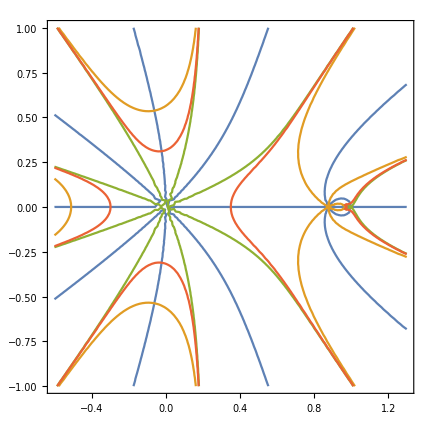

```mathematica
ContourPlot[{Im[f2[x+ⅈ y]]==-0.000001,Re[f2[x+ⅈ y]]==1,Re[f2[x+ⅈ y]]==0,Re[f2[x+ⅈ y]]==0.1},{x,-0.6,1.3},{y,-1,1},PerformanceGoal->"Quality"]
```